```mathematica
Log1[x_]:= If[x==0,0,Log2[Abs[x]]];
VEntropy[x_]:= -(x Log1[x] + (1-x)Log1[1-x]);
Prob[a_,b_,x_,y_]:= 1-(x^2y^2)/(a^2y^2+b^2x^2);
Cost[a_,b_,x_,y_] := VEntropy[x^2] + Prob[a,b,x,y];
Newa[a_,b_,x_,y_]:=((x^2-y^2)a*b)/(Sqrt[x^4b^2+y^4a^2]);
Cost2[a_,b_,x_,y_,x1_,y1_]:=  VEntropy[x^2] + Prob[a,b,x,y](Cost[Newa[a,b,x,y],Sqrt[1-Newa[a,b,x,y]^2],x1,y1])
Anlist = Anlist2={}
For[ar=0, ar<1,ar=ar+0.01,Anlist = Append[Anlist,{VEntropy[ar^2],NMinimize[{Cost2[ar,Sqrt[1-ar^2],x,Sqrt[1-x^2],x1,Sqrt[1-x1^2]],0≤x≤1&&0≤x1≤1},{x,x1},Method->"DifferentialEvolution"][[1]]}]]
For[ar=0, ar<1,ar=ar+0.01,Anlist2 = Append[Anlist2,{VEntropy[ar^2],NMinimize[{Cost[ar,Sqrt[1-ar^2],x,Sqrt[1-x^2]],0≤x≤1},{x},Method->"DifferentialEvolution"][[1]]}]]
```

{}

```mathematica
Anlist
```

{{0,0.},{0.00147303,0.0560441},{0.00509205,0.107775},{0.0104038,0.156715},{0.0171668,0.203349},{0.0252119,0.247962},{0.0344084,0.290751},{0.0446496,0.331865},{0.055845,0.371422},{0.0679161,0.409517},{0.0807931,0.446233},{0.0944136,0.481635},{0.108721,0.51578},{0.123662,0.548713},{0.139189,0.580269},{0.155256,0.60838},{0.171822,0.635391},{0.188845,0.661361},{0.206289,0.686341},{0.224116,0.71038},{0.242292,0.733521},{0.260785,0.755803},{0.279561,0.777262},{0.298591,0.797927},{0.317843,0.817827},{0.33729,0.836987},{0.356903,0.855426},{0.376654,0.873163},{0.396516,0.890208},{0.416464,0.906572},{0.43647,0.922256},{0.45651,0.937257},{0.476558,0.951563},{0.496589,0.965149},{0.51658,0.977974},{0.536505,0.989967},{0.55634,1.},{0.576062,1.},{0.595647,1.},{0.615071,1.},{0.63431,1.},{0.65334,1.},{0.672138,1.},{0.69068,1.},{0.708942,1.},{0.7269,1.},{0.74453,1.},{0.761807,1.},{0.778708,1.},{0.795207,1.},{0.811278,1.},{0.826897,1.},{0.842038,1.},{0.856674,1.},{0.870779,1.},{0.884325,1.},{0.897285,1.},{0.909631,1.},{0.921332,1.},{0.93236,1.},{0.942683,1.},{0.952271,1.},{0.96109,1.},{0.969108,1.},{0.97629,1.},{0.9826,1.},{0.988,1.},{0.992452,1.},{0.995917,1.},{0.998351,1.},{0.999711,1.},{0.999951,1.},{0.999023,1.},{0.996875,1.},{0.993452,1.},{0.988699,1.},{0.982554,1.},{0.974953,1.},{0.965824,1.},{0.955095,1.},{0.942683,1.},{0.928502,1.},{0.912455,1.},{0.894439,1.},{0.874337,1.},{0.852022,1.},{0.827349,1.},{0.800158,1.},{0.770262,1.},{0.737449,1.},{0.701471,1.},{0.662033,1.},{0.618776,1.},{0.571261,1.},{0.518923,0.979428},{0.46102,0.940537},{0.396516,0.890208},{0.323862,0.823855},{0.240455,0.731241},{0.140879,0.583324}}

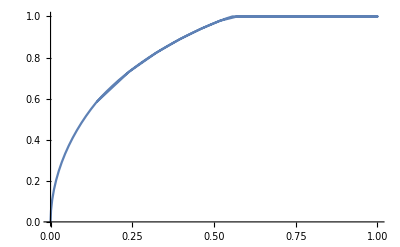

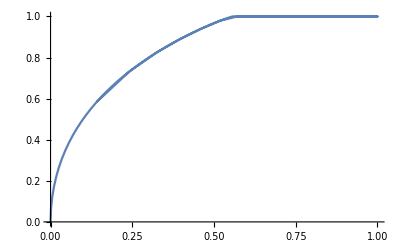

```mathematica
ListLinePlot[Anlist]
ListLinePlot[Anlist2]
```